```mathematica
ClearAll["Global`*"]
```

```mathematica
H=({{0, b1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {b1/2, -AC, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, b1/2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, b1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, b1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, b1/2, -AN-AC, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, b1/2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, b1/2, -AN, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, b1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, b1/2, +AN, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b1/2}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, b1/2, AN-AC}});
```

```mathematica
Clear[AN]
```

```mathematica
U=MatrixExp[-ⅈ*t*H]//FullSimplify;
U//MatrixForm
```

(ⅇ^((ⅈ AC t)/2) (Cos[1/2 √(AC^2+b1^2) t]-(ⅈ AC Sin[1/2 √(AC^2+b1^2) t])/(√(AC^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AC t)/2) Sin[1/2 √(AC^2+b1^2) t])/(√(AC^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(ⅈ b1 ⅇ^((ⅈ AC t)/2) Sin[1/2 √(AC^2+b1^2) t])/(√(AC^2+b1^2)) | ⅇ^((ⅈ AC t)/2) (Cos[1/2 √(AC^2+b1^2) t]+(ⅈ AC Sin[1/2 √(AC^2+b1^2) t])/(√(AC^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[(b1 t)/2] | -ⅈ Sin[(b1 t)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ Sin[(b1 t)/2] | Cos[(b1 t)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ((2.16+1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^((0.-0.25 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) t)+(-2.16-1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^((0.+0.25 ⅈ) (4.32+2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) t))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | (b1 ⅇ^((0.-0.25 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) t) (1.-1. ⅇ^((0.+0.5 ⅈ) √(18.6624+AC (17.28+4. AC)+4. b1^2) t)))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (b1 ⅇ^((0.-0.25 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) t) (1.-1. ⅇ^((0.+0.5 ⅈ) √(18.6624+AC (17.28+4. AC)+4. b1^2) t)))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | ((-2.16-1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^((0.-0.25 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) t)+(2.16+1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^((0.+0.25 ⅈ) (4.32+2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) t))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (ⅇ^(((0.+1.08 ⅈ)-0.5 √(-4.6656-1. b1^2)) t) ((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^(1. √(-4.6656-1. b1^2) t)))/(√(-4.6656-1. b1^2)) | -((0.+0.5 ⅈ) b1 ⅇ^(((0.+1.08 ⅈ)-0.5 √(-4.6656-1. b1^2)) t) (-1.+1. ⅇ^(1. √(-4.6656-1. b1^2) t)))/(√(-4.6656-1. b1^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -((0.+0.5 ⅈ) b1 ⅇ^(((0.+1.08 ⅈ)-0.5 √(-4.6656-1. b1^2)) t) (-1.+1. ⅇ^(1. √(-4.6656-1. b1^2) t)))/(√(-4.6656-1. b1^2)) | (ⅇ^(((0.+1.08 ⅈ)-0.5 √(-4.6656-1. b1^2)) t) ((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^(1. √(-4.6656-1. b1^2) t)))/(√(-4.6656-1. b1^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅇ^(((0.-1.08 ⅈ)-0.5 √(-4.6656-1. b1^2)) t) ((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^(1. √(-4.6656-1. b1^2) t)))/(√(-4.6656-1. b1^2)) | -((0.+0.5 ⅈ) b1 ⅇ^(((0.-1.08 ⅈ)-0.5 √(-4.6656-1. b1^2)) t) (-1.+1. ⅇ^(1. √(-4.6656-1. b1^2) t)))/(√(-4.6656-1. b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -((0.+0.5 ⅈ) b1 ⅇ^(((0.-1.08 ⅈ)-0.5 √(-4.6656-1. b1^2)) t) (-1.+1. ⅇ^(1. √(-4.6656-1. b1^2) t)))/(√(-4.6656-1. b1^2)) | (ⅇ^(((0.-1.08 ⅈ)-0.5 √(-4.6656-1. b1^2)) t) ((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^(1. √(-4.6656-1. b1^2) t)))/(√(-4.6656-1. b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((-2.16+1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^((0.-0.25 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) t)+(2.16-1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^((0.+0.25 ⅈ) (-4.32+2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) t))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2)) | (b1 ⅇ^((0.-0.25 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) t) (1.-1. ⅇ^((0.+0.5 ⅈ) √(18.6624+AC (-17.28+4. AC)+4. b1^2) t)))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (b1 ⅇ^((0.-0.25 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) t) (1.-1. ⅇ^((0.+0.5 ⅈ) √(18.6624+AC (-17.28+4. AC)+4. b1^2) t)))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2)) | ((2.16-1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^((0.-0.25 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) t)+(-2.16+1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^((0.+0.25 ⅈ) (-4.32+2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) t))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2)))

```mathematica
Uc1=U/.t->n*π/b1//FullSimplify;
Uc1//MatrixForm
```

(ⅇ^((ⅈ AC n π)/(2 b1)) (Cos[(√(AC^2+b1^2) n π)/(2 b1)]-(ⅈ AC Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AC n π)/(2 b1)) Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(ⅈ b1 ⅇ^((ⅈ AC n π)/(2 b1)) Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2)) | ⅇ^((ⅈ AC n π)/(2 b1)) (Cos[(√(AC^2+b1^2) n π)/(2 b1)]+(ⅈ AC Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[(n π)/2] | -ⅈ Sin[(n π)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ Sin[(n π)/2] | Cos[(n π)/2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ((2.16+1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^(-((0.+0.785398 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1)+(-2.16-1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^(((0.+0.785398 ⅈ) (4.32+2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | (b1 ⅇ^(-((0.+0.785398 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1) (1.-1. ⅇ^(((0.+1.5708 ⅈ) √(18.6624+AC (17.28+4. AC)+4. b1^2) n)/b1)))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (b1 ⅇ^(-((0.+0.785398 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1) (1.-1. ⅇ^(((0.+1.5708 ⅈ) √(18.6624+AC (17.28+4. AC)+4. b1^2) n)/b1)))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | ((-2.16-1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^(-((0.+0.785398 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1)+(2.16+1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^(((0.+0.785398 ⅈ) (4.32+2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (ⅇ^((((0.+3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) ((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | -((0.+0.5 ⅈ) b1 ⅇ^((((0.+3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) (-1.+1. ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -((0.+0.5 ⅈ) b1 ⅇ^((((0.+3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) (-1.+1. ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | (ⅇ^((((0.+3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) ((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅇ^((((0.-3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) ((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | -((0.+0.5 ⅈ) b1 ⅇ^((((0.-3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) (-1.+1. ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -((0.+0.5 ⅈ) b1 ⅇ^((((0.-3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) (-1.+1. ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | (ⅇ^((((0.-3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) ((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((-2.16+1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^(-((0.+0.785398 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1)+(2.16-1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^(((0.+0.785398 ⅈ) (-4.32+2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2)) | (b1 ⅇ^(-((0.+0.785398 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1) (1.-1. ⅇ^(((0.+1.5708 ⅈ) √(18.6624+AC (-17.28+4. AC)+4. b1^2) n)/b1)))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (b1 ⅇ^(-((0.+0.785398 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1) (1.-1. ⅇ^(((0.+1.5708 ⅈ) √(18.6624+AC (-17.28+4. AC)+4. b1^2) n)/b1)))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2)) | ((2.16-1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^(-((0.+0.785398 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1)+(-2.16+1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^(((0.+0.785398 ⅈ) (-4.32+2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2)))

```mathematica
Transpose[Conjugate[Uc1]].Uc1//ComplexExpand//Simplify//MatrixForm
```

```mathematica
Rz1=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ((-1)^n)*-ⅈ, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ((-1)^n)*-ⅈ, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
Uc2=Rz1.Uc1//FullSimplify;
Uc2//MatrixForm
```

(ⅇ^((ⅈ AC n π)/(2 b1)) (Cos[(√(AC^2+b1^2) n π)/(2 b1)]-(ⅈ AC Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2))) | -(ⅈ b1 ⅇ^((ⅈ AC n π)/(2 b1)) Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2)) | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0
-(ⅈ b1 ⅇ^((ⅈ AC n π)/(2 b1)) Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2)) | ⅇ^((ⅈ AC n π)/(2 b1)) (Cos[(√(AC^2+b1^2) n π)/(2 b1)]+(ⅈ AC Sin[(√(AC^2+b1^2) n π)/(2 b1)])/(√(AC^2+b1^2))) | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0
0 | 0 | -ⅈ (-1)^n Cos[(n π)/2] | -(-1)^n Sin[(n π)/2] | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0
0 | 0 | -(-1)^n Sin[(n π)/2] | -ⅈ (-1)^n Cos[(n π)/2] | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0
0 | 0 | 0 | 0 | ((2.16+1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^(-((0.+0.785398 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1)+(-2.16-1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^(((0.+0.785398 ⅈ) (4.32+2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | (b1 ⅇ^(-((0.+0.785398 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1) (1.-1. ⅇ^(((0.+1.5708 ⅈ) √(18.6624+AC (17.28+4. AC)+4. b1^2) n)/b1)))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0
0 | 0 | 0 | 0 | (b1 ⅇ^(-((0.+0.785398 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1) (1.-1. ⅇ^(((0.+1.5708 ⅈ) √(18.6624+AC (17.28+4. AC)+4. b1^2) n)/b1)))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | ((-2.16-1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^(-((0.+0.785398 ⅈ) (-4.32-2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1)+(2.16+1. AC+0.5 √(18.6624+AC (17.28+4. AC)+4. b1^2)) ⅇ^(((0.+0.785398 ⅈ) (4.32+2. AC+1. √(18.6624+AC (17.28+4. AC)+4. b1^2)) n)/b1))/(√(18.6624+AC (17.28+4. AC)+4. b1^2)) | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (ⅇ^((((0.+3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) ((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | -((0.+0.5 ⅈ) b1 ⅇ^((((0.+3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) (-1.+1. ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -((0.+0.5 ⅈ) b1 ⅇ^((((0.+3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) (-1.+1. ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | (ⅇ^((((0.+3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) ((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | (ⅇ^((((0.-3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) ((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | -((0.+0.5 ⅈ) b1 ⅇ^((((0.-3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) (-1.+1. ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | -((0.+0.5 ⅈ) b1 ⅇ^((((0.-3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) (-1.+1. ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | (ⅇ^((((0.-3.39292 ⅈ)-1.5708 √(-4.6656-1. b1^2)) n)/b1) ((0.+1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)+((0.-1.08 ⅈ)+0.5 √(-4.6656-1. b1^2)) ⅇ^((3.14159 √(-4.6656-1. b1^2) n)/b1)))/(√(-4.6656-1. b1^2)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | ((-2.16+1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^(-((0.+0.785398 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1)+(2.16-1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^(((0.+0.785398 ⅈ) (-4.32+2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2)) | (b1 ⅇ^(-((0.+0.785398 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1) (1.-1. ⅇ^(((0.+1.5708 ⅈ) √(18.6624+AC (-17.28+4. AC)+4. b1^2) n)/b1)))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2))
0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | (b1 ⅇ^(-((0.+0.785398 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1) (1.-1. ⅇ^(((0.+1.5708 ⅈ) √(18.6624+AC (-17.28+4. AC)+4. b1^2) n)/b1)))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2)) | ((2.16-1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^(-((0.+0.785398 ⅈ) (4.32-2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1)+(-2.16+1. AC+0.5 √(18.6624+AC (-17.28+4. AC)+4. b1^2)) ⅇ^(((0.+0.785398 ⅈ) (-4.32+2. AC+1. √(18.6624+AC (-17.28+4. AC)+4. b1^2)) n)/b1))/(√(18.6624+AC (-17.28+4. AC)+4. b1^2)))

```mathematica
Rz2=({{((-1)^m)*ⅇ^(-(ⅈ AC n π)/(2 b1)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ((-1)^m)*ⅇ^(-(ⅈ AC n π)/(2 b1)), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ((-1)^q)*ⅇ^(-(ⅈ (AC+AN) n π)/(2 b1)), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ((-1)^q)*ⅇ^(-(ⅈ (AC+AN)n π)/(2 b1)), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ((-1)^l)*ⅇ^(-(ⅈ AN n π)/(2 b1)), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, ((-1)^l)*ⅇ^(-(ⅈ AN n π)/(2 b1)), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, ((-1)^l)*ⅇ^((ⅈ AN n π)/(2 b1)), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ((-1)^l)*ⅇ^((ⅈ AN n π)/(2 b1)), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ((-1)^k)*ⅇ^(-(ⅈ (AN-AC) n π)/b1), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ((-1)^k)*ⅇ^(-(ⅈ (AN-AC) n π)/b1)}});
```

```mathematica
Uc3=Rz2.Uc2 //FullSimplify;
Uc3 // MatrixForm;
```

```mathematica
Ucnot=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
FavRaw=(Abs[Tr[Ucnot.Uc3]]^2+12)/156//FullSimplify//ComplexExpand
```

```mathematica
FavRaw1=FavRaw/.{AN->2.16,AC->0.43};
```

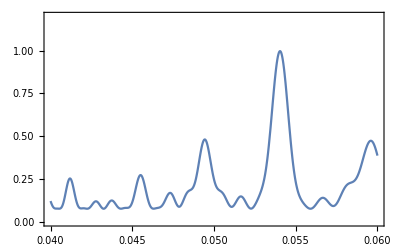

```mathematica
Plot[{FavRaw1}/.{n->1,m->2,k->2,l->2,q->2,p->2},{b1,0.04,0.06},PlotRange->{0,1.2},Frame->True]
```